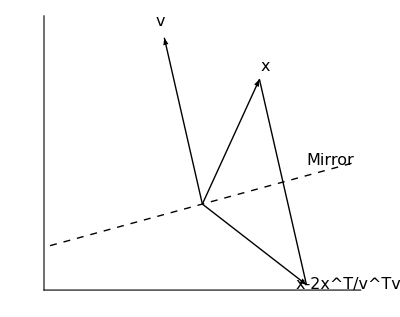

```mathematica
householder=Show[Graphics[Arrow[{{0,0},{3/4,3/2}}]],Graphics[Arrow[{{0,0},{-1/2,2}}]],Graphics[Arrow[{{0,0},{3/4,3/2}-2({3/4,3/2}.{-1/2,2})/({-1/2,2}.{-1/2,2}){-1/2,2}}]],Graphics[Line[{{3/4,3/2}-2({3/4,3/2}.{-1/2,2})/({-1/2,2}.{-1/2,2}){-1/2,2},{3/4,3/2}}]],Graphics[{Dashed,Line[{{-2,-1/2},{2,1/2}}]}],Graphics[Text[Style["x",16,Italic,FontFamily->"Times"],1.1{3/4,3/2}]],Graphics[Text[Style["v",16,Italic,FontFamily->"Times"],1.1{-1/2,2}]],Graphics[Text[Style["x-2x^T/v^Tv",16,Italic,FontFamily->"Times"],{1.4,1}({3/4,3/2}-2({3/4,3/2}.{-1/2,2})/({-1/2,2}.{-1/2,2}){-1/2,2})]],Graphics[Rotate[Text[Style["Mirror",16,Italic,FontFamily->"Times"],{7/4,1/10}],ArcTan[1/2/2],{0,0}]],Axes->True,Ticks->None,PlotRange->All(*{{-2,2},{-5/4,3}}*)]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/barry/Documents/Teaching/ACM30100 - Mathematics of Machine Learning/Learning Materials/ACM30100-Examples/Matrix Factorisation

```mathematica
Export["Householder.png",householder,ImageResolution->100]
```

Householder.png